# 后疫情时代及COVID-19突变株影响与周期性的研究

中山大学 物理学院 
郭蒙 20343097

## 1. 前言

### 1.1 背景介绍

自2020年初COVID-19爆发以来，国际形势大变，并且对国际金融造成了重创。尽管这近两年以来对该问题，无论是传染病模型还是国际经济发展的研究都已经比较详细和全面。但是COVID-19的突变株相继出现，对整个国际形势仍然有决定性的影响，我们尝试重复一些较为简单的拟合研究，并且尝试找到引起国际注意的高传染性突变株出现的周期性规律并分析。

### 1.2 研究方法

本文通过利用Mathematica集数据处理分析、符号拟合运算和Wolfram丰富的数据库的支撑，辅以其他渠道得到的.csv文件的数据，在Mathematica中利用可视化和其他功能运算进行分析并得出结论。

## 2. 病毒初期中国湖北省疫情病例曲线及建模

### 2.1 数据导入和分类

利用Wolfram DataBase中自带的Wolfram DataSet格式的数据库直接进行数据抓取

```mathematica
DeleteObject[
ResourceObject["Epidemic Data for Novel Coronavirus COVID-19"]]
```

```mathematica
(*删除缓存的对象以便于导入最新的数据*)
```

```mathematica
datacn=ResourceData["Epidemic Data for Novel Coronavirus COVID-19","ChinaProvinces"]
(*导入中国疫情表 数据范围——自2020.1.22到2021.12.12*)
```

Dataset[<>]

我们只对疫情爆发初期的曲线感兴趣，我们将中国湖北省自2020.1.22至2020.4.30日的确诊、死亡和治愈的病例进行提取

```mathematica
templist=
Normal@
datacn[SelectFirst[#AdministrativeDivision==LinguisticAssistant&],
{#ConfirmedCases-(#RecoveredCases+#Deaths),#RecoveredCases,#Deaths}&];
(*截断时间至我们将要研究的时间*)
{Hubeiinfected,Hubeirecovered,Hubeideceased}=
TimeSeriesWindow[#,{{2020,1,22},{2020,4,30}}]&/@templist
```

{TimeSeries[…],TimeSeries[…],TimeSeries[…]}

### 2.2 数据整体可视化

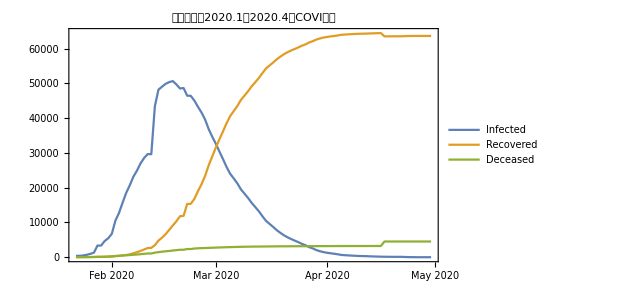

```mathematica
DateListPlot[{Hubeiinfected,Hubeirecovered,Hubeideceased},
PlotLabel->"中国湖北省2020.1至2020.4间COVID-19数据",
PlotLegends->{"Infected","Recovered","Deceased"}]
```

### 2.3 使用SIR模型进行拟合

下面利用传染病动力学中最为经典的SIR模型对该组数据进行拟合，下面简要介绍一下SIR模型——SIR模型的建立基于以下三个假设：
	- 不考虑人口的出生、死亡、流动等种群动力因素。人口始终保持一个常数，即N(t)≡K
	- 一个病人一旦与易感者接触就必然具有一定的传染力。假设 t 时刻单位时间内，一个病人能传染的易感者数目与此环境内易感者总数s(t)成正比，比例系数为β，从而在t时刻单位时间内被所有病人传染的人数为βs(t)。
	-t 时刻，单位时间内从染病者中移出的人数与病人数量成正比，比例系数为γ，单位时间内移出者的数量为γi(t)
	基于以上假设，我们有感染机制的模型描述
							-Graphics-
	基于以上理论，我们给出微分方程形式的SIR模型并用于拟合

```mathematica
odeSIR={𝒮'[t]==-β 𝒮[t] ℐ[t]/𝒩,ℐ'[t]==β 𝒮[t] ℐ[t]/𝒩-γ ℐ[t],ℛ'[t]==γ ℐ[t]};
(*在给定t=0时刚出现感染情况的初值情况下，获得参数数值解*)
pmNDSolve=ParametricNDSolve[{odeSIR,𝒮[0]==𝒩-i0,ℐ[0]==i0,ℛ[0]==0},{𝒮,ℐ,ℛ},{t,0,100},{𝒩,i0,β,γ}];
(*回代至ODE中*)
{solI,solR}={ℐ,ℛ}/.pmNDSolve
```

{ParametricFunction[<>],ParametricFunction[<>]}

```mathematica
(*定义拟合模型*)
fitModelSIR[𝒩_,β_,γ_][tag_,t_]:= Which[tag==1,solI[𝒩,1,β,γ][t],tag==2,solR[𝒩,1,β,γ][t]]
```

由于前文的数据仍是含时间序列的列表，需要改写为顺序序列的列表才能参与拟合

```mathematica
Length[Normal@Hubeiinfected]
```

100

```mathematica
HubeiinfectedData=MapIndexed[{#2⟦1⟧,#1}&][Hubeiinfected["Values"]]⟦;;100⟧;
HubeideceasedData=MapIndexed[{#2⟦1⟧,#1}&][Hubeideceased["Values"]]⟦;;100⟧;
```

整合在统一同一数据集中

```mathematica
dataSIR=Join[Prepend[#,1]&/@HubeiinfectedData,
Prepend[#,2]&/@HubeirecoveredData];
```

```mathematica
fitSIR=NonlinearModelFit[dataSIR,fitModelSIR[𝒩,β,γ][tag,t],{{𝒩,12000},{β,0.27},{γ,0.03}},{tag,t}];
(*拟合后给出可能的参数条件*)
```

```mathematica
fitSIR["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
𝒩 | 67613.3 | 726.955 | 93.0089 | 1.00305×10^-164
β | 0.563189 | 0.00669564 | 84.1127 | 2.46842×10^-156
γ | 0.0458924 | 0.0012546 | 36.5794 | 9.02522×10^-90

```mathematica
fitSIR["BestFitParameters"]
```

{𝒩→67613.3,β→0.563189,γ→0.0458924}

在最佳参数下绘出拟合图像

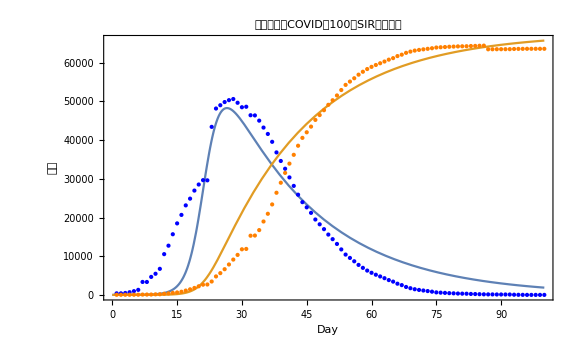

```mathematica
Plot[{solI[𝒩,1,β,γ][t]/. fitSIR["BestFitParameters"],solR[𝒩,1,β,γ][t]/. fitSIR["BestFitParameters"]},{t,0,100},

Epilog:>{Blue,Point@HubeiinfectedData,Orange,Point@HubeirecoveredData},
Frame->True,
FrameLabel->{"Day","人数"},
PlotLabel->"中国湖北省COVID-19前100天SIR拟合数据",
ImageSize->Large]
```

由上图可知，在拟合模型下，对于峰值和拐点有着较为合理的预测，但是在过渡部分仍然不太准确，是真实情况过于复杂和拟合模型的参数数量较少所致的。我们可以看见，在Day21左右，确诊病例因为重新统计更新有着较大的改变，在其余位置，对模型的拟合还是较为准确的。

### 2.4 拟合模型的分析与展望

在上文我们采用了SIR中最为简单的拟合形式，我们不得不承认尽管对于理想模型来讲其微分方程的形式已经较为复杂，但是对与真实事件的模拟还是略显无力，可以看见，上图在基本趋势和峰值位置上已经和真实情况略为接近。对于SIR模型，还有增加单位时间治愈人数的参数变量，但是本文的重心并不在单一优化传染病模型上，对于一年前的疫情数据，在互联网上已经能够轻易的找到模型更为精确的拟合，我们在此不在重复。只是通过一个较为简单的例子展现Mathematica集数据收集、处理、分析和可视化为一体的能力，接下来我们会分析在各国防疫政策已基本稳定和COVID在Delta变异株和OmiCron变异株影响下其他值得研究的特征。

## 3. Delta和Omicron变异株对各国COVID-19曲线的影响

### 3.1 基本介绍和数据处理

新冠疫情在2021年的国际防控形式已经逐渐常态化，但是隔一段时间就会有的突变株对国际防控形式会起到决定性的作用，尽管其重病率和死亡率在医疗条件稳定的情况下已经较为乐观，但是其高传染性给各国带来的压力仍然不少。
	下面以Delta和Omicron变异株为例，尝试寻找出COVID-19突变的规律和其他特征。

### 3.2 近一年来的世界确诊病例曲线

获取数据集中世界国家的确诊曲线并处理

```mathematica
wdData=ResourceData["Epidemic Data for Novel Coronavirus COVID-19","WorldCountries"];
```

我们以美国和英国为例，做出2020.9.1-2021.12.12的数据曲线

```mathematica
UsAndUkConfirmedCases=wdData[
Select[#Country==LinguisticAssistant||#Country==LinguisticAssistant&],
{#Country,#ConfirmedCases}&]
```

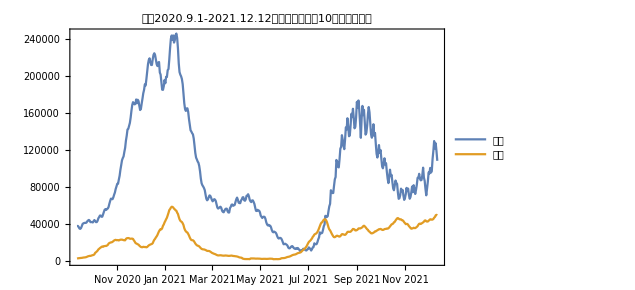

```mathematica
DateListPlot[
{MovingAverage[
Differences[
TimeSeriesWindow[UsAndUkConfirmedCases[1,2],
{{2020,9,1},{2021,12,12}}]]
,10],
MovingAverage[
Differences[
TimeSeriesWindow[UsAndUkConfirmedCases[2,2],
{{2020,9,1},{2021,12,12}}]]
,10]},
PlotLabel->"美英2020.9.1-2021.12.12单日新增曲线（10天移动平均）",
PlotLegends->{"美国","英国"}]
```

```mathematica
(*第一次尝试寻找是否存在周期性规律*)
Fourier[
UsAndUkConfirmedCases[1,2]["Values"]]//Abs//ListLinePlot
```

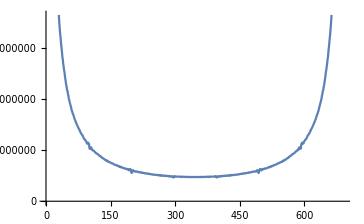
```mathematica
-Graphics-
(*未能获得明显的周期性结果*)
```

通过查询资料得到，Delta变异株于2020.10在印度被发现，以高传染性著称；
Omicron于2021.12月在南非发现，后面我们简单比较一下Delta和Omicron在爆发地的确诊曲线。

### 3.2 Delta突变株爆发地曲线

```mathematica
IndiaConfirmCases=wdData[
Select[#Country==LinguisticAssistant&],
{#Country,#ConfirmedCases}&];
IndiaConfirmCasestimeWindow=TimeSeriesWindow[
IndiaConfirmCases[1,2],
{{2020,9,1},{2021,1,1}}]
```

TimeSeries[…]

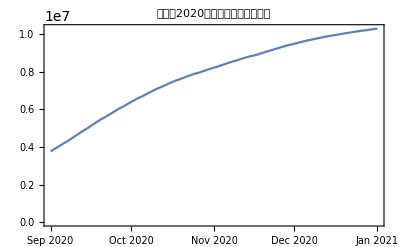

```mathematica
DateListPlot[IndiaConfirmCasestimeWindow,
PlotLabel->"印度于2020年第四季度总感染曲线"]
```

我们发现在爆发当时并没有达到感染率高发期，我们进一步拉宽时间进行分析

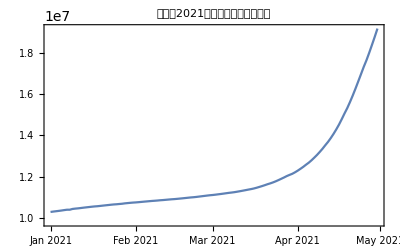

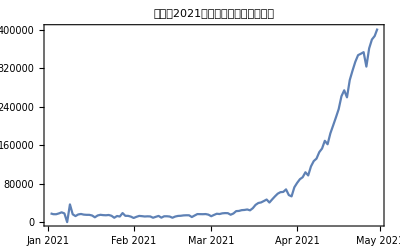

```mathematica
IndiaConfirmCasestimeWindow2=TimeSeriesWindow[
IndiaConfirmCases[1,2],
{{2021,1,1},{2021,4,30}}];
DateListPlot[%,
PlotLabel->"印度于2021年第一季度总感染曲线"]
DateListPlot[Differences[IndiaConfirmCasestimeWindow2],
PlotLabel->"印度于2021年第一季度单日感染曲线"]
```

考虑到病毒从发现到爆发的延迟期，由于各国的医疗水平和条件不一样，我们无法预知不	同国家发现新突变病毒的能力。但是值得注意的是，上图分别为总增长曲线和每日新增曲线，但是两者走势近乎一样，说明单日新增的量级已经和总体量相当！

### 3.3 Omicron突变株爆发地曲线

```mathematica
SouthAfConfirmedCases=wdData[
Select[#Country==LinguisticAssistant&]
,{#Country,#ConfirmedCases}&]
```

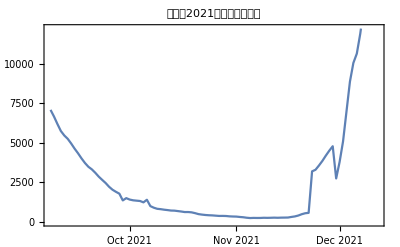

```mathematica
DateListPlot[MovingAverage[
Differences[
TimeSeriesWindow[SouthAfConfirmedCases[1,2],
{{2021,9,1},{2021,12,12}}]],7],
PlotLabel->"南非在2021年末的新增曲线"]
```

Omicron变异株从发现到爆发的时间远远低于印度的Delta变异株，这一方面可能是两个国家人口基数和医疗条件的差别，当然也有其他（包括气候等因素）的影响，但是由于变量太过复杂，最重要的原因是我们暂时还无法预知OmiCron的传染峰值是否已经来到（因为2021.12才于南非发现）我们暂无法进行进一步讨论。

### 3.4 世界疫情曲线的周期性（突变周期性）的分析与预测

我们在研究上节的时候发现南非的确诊曲线有着极为良好的周期性

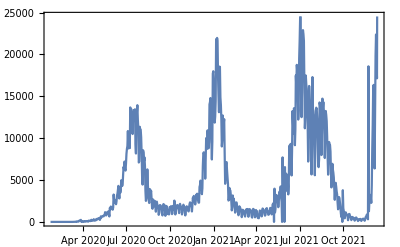

```mathematica
SouthAfConfirmedCases[1,2]//Differences//DateListPlot
```

（图中有一个很有意思的现象，在具有较为良好的周期性的同时，每次大规模的感染时的峰值总是逐渐拔高，变相暗示了每个突变株的感染能力逐渐升高，这是很不乐观的一件事）
	我们猜测，在南非这样的医疗水平较为低下的国家，政府医疗系统对疫情的干涉能力非常小，且疫苗接种率仍然较低，一定程度上能反映较为简单的卫生条件的情况下病毒传染的性质。
	我们使用傅立叶变换对单日新增的数据进行周期性分析，这里需要注意的是，由于每日的波动不能客观的反映一段时间的趋势，我们使用合理移动平均对其先进行处理。

```mathematica
(*将时间序列转化为一般值序列*)
SouthAfConfirmedCasesValue=SouthAfConfirmedCases[1,2]["Values"];
%//Short
```

{0,0,0,0,0,0,«679»,3051222,3071064,3093452,3112469,3129622,3167497}

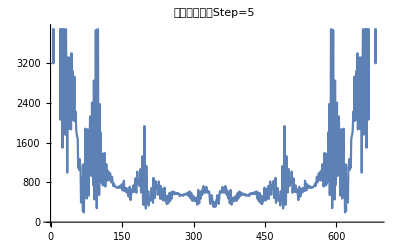
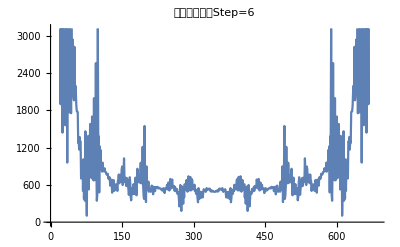
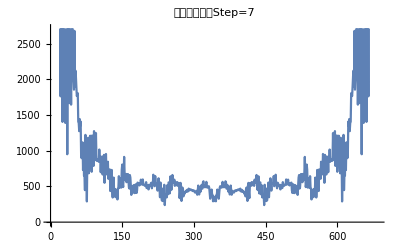
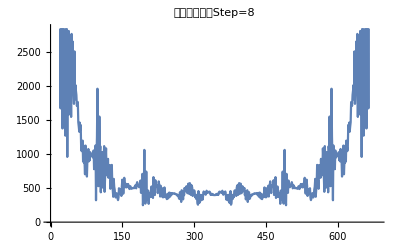
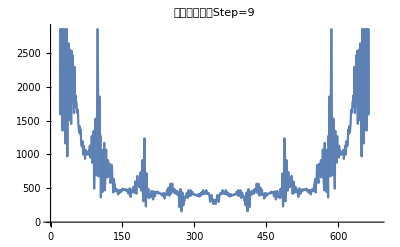
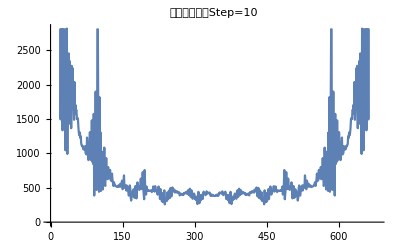

```mathematica
Table[
ListLinePlot[Fourier[
MovingAverage[
Differences[SouthAfConfirmedCasesValue],step]]//Abs,
PlotLabel->"移动平均步长Step="<>ToString[step]],
{step,5,10,1}]
```

我们发现有四个突出的峰经常出现，大约在100、200、500、600天之间，由于COVID-19出现时间仅仅在2年左右，对于我们现在的数据而言，我们舍掉大于一年的可能周期，在100、200天之间，我们选择周期特征更大的100天，并且取移动平均的平均步长为5时，绘出更细节的图像。

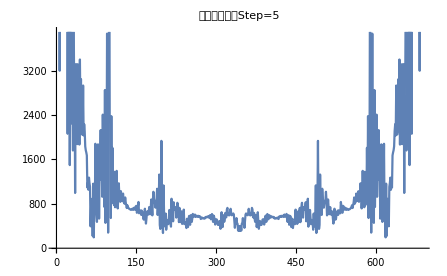

```mathematica
ListLinePlot[Fourier[
MovingAverage[
Differences[SouthAfConfirmedCasesValue],5]]//Abs,
PlotLabel->"移动平均步长Step="<>ToString[5]]
```

在所选择的南非样本中，我们根据已知数据认为COVID-19在以非洲为代表的低医疗水平地区，每一次新增的峰值的周期在100天左右。

## 4*. COVID-19对航班的影响

我们在国际民用航空组织上下载了2020年（缺少11、12月，最新的数据还未更新）美国的各月的航班人数。

```mathematica
(*导入文件为Dataset格式*)
UsaAirlineData=Import["/Users/menakuniay/Desktop/tempairdata.csv",
"Dataset",
HeaderLines->1]
```

Dataset[<>]

```mathematica
(*下面使用Table函数分别提取自2018年以来各月的航班总人数*)
(*使用Select函数对数据进行提取和合并*)
SumPassengersUsa=Table[UsaAirlineData[
Select[#[[16]]==year&& #[[17]]==month&],
#[[1]]&]//Total,{year,2018,2020},{month,1,12}]
```

```mathematica
{{16563412,15169649,19393935,19009785,20138742,20868853,21457736,20476253,17497945,19678863,19051637,18829148},{16857305,15560395,19634813,19305834,20405211,20847922,21330406,20414740,18385639,19745311,18036903,19471563},{16804782,15677289,8645905,724287,2000367,4980362,5612023,5694449,5361418,5822046,0,0}}
```

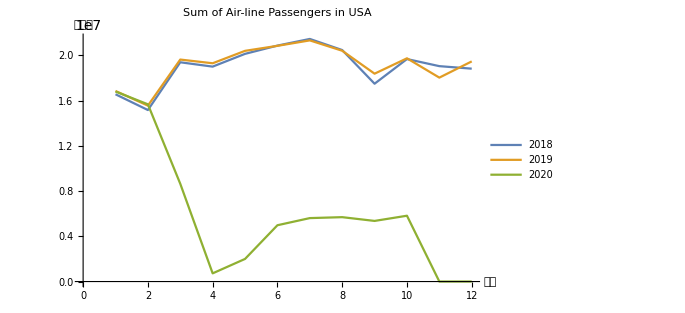

```mathematica
{SumPassengersUsa2018,SumPassengersUsa2019,SumPassengersUsa2020}=SumPassengersUsa;
ListLinePlot[
{SumPassengersUsa2018,SumPassengersUsa2019,SumPassengersUsa2020},
PlotLegends->{"2018","2019","2020"},
PlotLabel->"Sum of Air-line Passengers in USA",
AxesLabel->{"月份","客流量"}]
```

可以直观的看到，2018年和2019年的人流量基本持平，2020年1月和2月也和往年持平，但从3月开始一直下降，下降到4月达到最低值，仅为2019年同期的

```mathematica
ToString[N[SumPassengersUsa2020[[4]]/SumPassengersUsa2019[[4]]] 10^3]<>"%"
```

37.5165%

直到6月客流量开始逐渐回升，但是仍不及同期的一半，但是我们缺少2021年最新的数据，缺少对后疫情时代稳定的航班客流量的分析，留有一部分遗憾。

## 5. 小结

我们通过SIR传染病模型简单的复现了COVID-19爆发初期在爆发地的各项曲线，并且得到了较为准确的拟合图形，说明了疫情的发展仍可以用客观的数学模型所描述。然后通过研究以美国、英国为代表的发达国家和国际人流量流通较大的国家近一年的疫情曲线，无法得到较为合理的周期性关系，我们认为是发达国家的医疗资源充足对一段时间的高爆发传染期有着抑制作用。然后Delta毒株爆发地印度的曲线过于极端，在2021年第一季度有着令人咂舌的爆发式增长、然而这一数据也不能客观的表示周期性规律。
	医疗资源尚不发达、作为非洲国家的南非，是2021年末OmiCron毒株的爆发地，自2021年12以来，其增长曲线也是一骑绝尘，侧面反映了本次Omicron的高传染性引起强烈国际注意的原因。并且南非曲线有着非常明显周期性，通过FFT分析认为每次大规模高传染性COVID-19变异株的爆发周期在100天左右，且传染时日增峰值逐渐增高。按此规律，那么2022年4月左右将会迎来新一个传染性较高的变异株，我们希望疫苗的发展可以抑制这种事件的发生，但我们也必须要有所准备。
	最后本文简单的以美国航空总人流量的变化在体现COVID-19对人类社会经济打击之大，希望引起人们的重视。由于部分数据敏感和数据更新的不及时，本文有部分分析工作无法开展，在以后将会有更多数据供人类以分析，可以得出更科学更有信服力的规律助以COVID-19的研究之中。

## 参考文献

Wolfram language reference https://reference.wolfram.com/language/

COVID-19 Data Analysis and Visualization, Wolfram U https://www.wolfram.com/wolfram-u/covid-data-analysis-and-visualization/

FFT in Mathematica Q&A https://mathematica.stackexchange.com/questions/192193/which-fft-algorithm-does-fourier-use

COVID-19 Data Repository by the Center for Systems Science and Engineering (CSSE) at Johns Hopkins University https://github.com/CSSEGISandData/COVID-19

2019冠状病毒病. (2021, December 12). Retrieved from 维基百科, 自由的百科全书: https://zh.wikipedia.org/w/index.php?title=2019%E5%86%A0%E7%8A%B6%E7%97%85%E6%AF%92%E7%97%85&oldid=69066021

IMF World Economic Outlook Database https://www.imf.org/en/home